```mathematica
ConfidenceInterval[list_,α_]:=Module[{t,x},
{Subtract@@#,Plus@@#}&@Flatten[{Mean[list],Evaluate[Select[Flatten[t/.NSolve[Integrate[PDF[StudentTDistribution[Length[list]-1],x],{x,-t,t}]==1-α,t]],Positive]]*StandardDeviation[list]/Sqrt[Length[list]-1]}]];
ConfidenceInterval[n_,mean_,s_,α_]:=Module[{t,x},
{Subtract@@#,Plus@@#}&@Flatten[{mean,Select[Flatten[t/.NSolve[Integrate[PDF[StudentTDistribution[n-1],x],{x,-t,t}]==1-α,t]],Positive]*s/Sqrt[n-1]}]];
(*Better if n is odd*)
uTest[n_,mean_,μ_,σ_,α_]:=Abs[mean-μ]/σ*Sqrt[n]<Select[x/.Solve[CDF[NormalDistribution[],x]==1-α/2,x]//Quiet];
uTest[list_,μ_,σ_,α_]:=Abs[Mean[list]-μ]/σ*Sqrt[Length[list]]<First[x/.Solve[CDF[NormalDistribution[],x]==1-α/2,x]//Quiet];
FTest[list1_,list2_,α_]:=(Divide@@(StandardDeviation/@#))<First[x/.NSolve[CDF[FRatioDistribution[Length[First[#]]-1,Length[Last[#]]-1],x]==1-α/2]]&[Sort[{list1,list2},StandardDeviation[#1]>StandardDeviation[#2]&]]//Quiet;
tTest[list1_,list2_,α_]:=Module[{sp,n1,n2,s1,s2,x},
n1=Length[list1];
n2=Length[list2];
s1=StandardDeviation[list1];
s2=StandardDeviation[list2];
sp=Sqrt[((n1-1)*s1^2+(n2-1)*s2^2)/(n1+n2-2)];
If[FTest[list1,list2,α],
Abs[Mean[list1]-Mean[list2]]/sp Sqrt[n1*n2/(n1+n2)]<First[Select[x/.Solve[CDF[StudentTDistribution[n1+n2-2],x]<1-α/2,x],Positive]]

,"FTest False"]];

IonDistribution[H_,KaList_]:=Reverse@Table[(H^i*(Times@@Drop[KaList,-i]))/Sum[H^i*(Times@@Drop[KaList,-i]),{i,0,Length[KaList]}],{i,0,Length[KaList]}];
(*Sample: IonDistribution[1,{0.8,10^-4}]*)
H[density_,KaList_]:=Quiet[
Module[{H},
Last[H/.
Solve[density*Total[Table[i,{i,0,Length[KaList]}].IonDistribution[H,KaList]]+10^-14/H==H,H]
]
]
];
pH[density_,KaList_]:=-Log[H[density,KaList]];
(*Example: pH[1.8,{0.8,10^-4}]*)
MixH[KaList_]:=Quiet[
Module[{H},
Last[H/.
Solve[Total[#1*Total[Table[i,{i,0,Length[#2]}].IonDistribution[H,#2]]&@@@KaList]+10^-14/H==H,H]
]
]
];
(*Example: MixH[{{1,{0.01,10^-5}},{2,{10^-4,10^-6,10^-8}}}]*)
KaListConvert[KaList_]:=Reverse[Times@@@NestList[Drop[#,-1]&,KaList,Length[KaList]-1]];
BetaListConvert[BetaList_]:=Prepend[1/#&/@Divide@@@Subsequences[BetaList,{2}],First[BetaList]];
BetaIonDistribution[ligand_,BetaList_]:=#/Total[#]&[DiagonalMatrix[Table[ligand^i,{i,0,Length[BetaList]}]].Prepend[BetaList,1]];
ProtonEquation[densityList_]:=(Plus@@DiagonalMatrix[densityList].Table[Range[Length[densityList]]-i,{i,Length[densityList]}])/Total[densityList];(*Example:ProtonEquation[{0,2,3}],whose result is {-8/5,-3/5,2/5}, which follows the electrolyzing order*)
ComplexH[density_,KaList_]:=Quiet[
First@Select[Module[{H},
H/.NSolve[Total[density]*ProtonEquation[density].IonDistribution[H,KaList]+10^-14/H==H,H]
]
,Positive]];
(*Example: ComplexH[{3,2,2},{10^-3,10^-7}]  Note that there is one more data required in density list than Ka list*)

IntegralH[list_]:=Quiet[
Select[Module[{H},
Re[H/.Solve[Total[Total[#1]*ProtonEquation[#1].IonDistribution[H,#2]&@@@list]+10^-14/H==H,H]
]]
,Positive]];
(*Example: IntegralH[{{{3,2,3},{10^-3,10^-7}},{{0,4},{10^-8}}}]*)
Coordination[ligand_,center_,BetaList_]:=Module[{x,list,a},list=x/.NSolve[center*(Table[-i,{i,0,Length[BetaList]}].BetaIonDistribution[x,BetaList])+ligand==x,x];
a=First[Select[Re@list,Positive]]//Quiet;
center*First[BetaIonDistribution[a,BetaList]]
];
```

```mathematica
IonDistribution[10^-7,{10^-2.16,10^-7.21,10^-12.32}]
```

{8.94116×10^-6,0.618577,0.381412,1.82555×10^-6}

```mathematica
0.618577*0.1
```

0.0618577

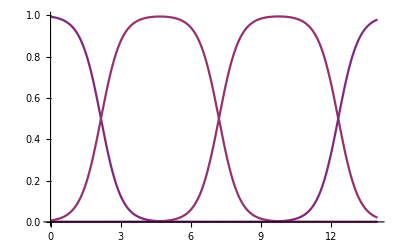

```mathematica
Plot[IonDistribution[10^-x,{10^-2.16,10^-7.21,10^-12.32}],{x,0,14},ColorFunction->"Rainbow"]
```

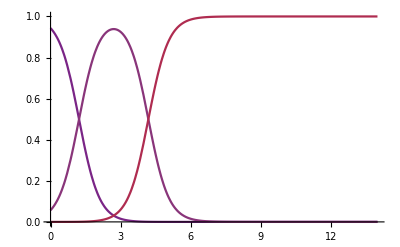

```mathematica
Plot[IonDistribution[10^-x,{10^-1.22,10^-4.19}],{x,0,14},ColorFunction->"Rainbow"]
```

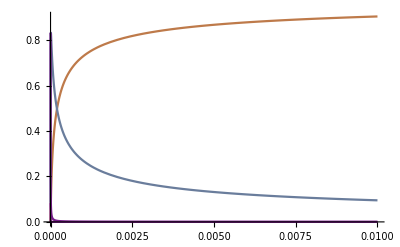

```mathematica
Plot[IonDistribution[H[x,#],#]&[{10^-4,10^-6,10^-8}],{x,0,0.01},ColorFunction->"Rainbow"]
```

```mathematica
IntegralH[{{{3,2,3},{10^-3,10^-7}},{{0,4},{10^-8}}}]
```

1.17044×10^-7

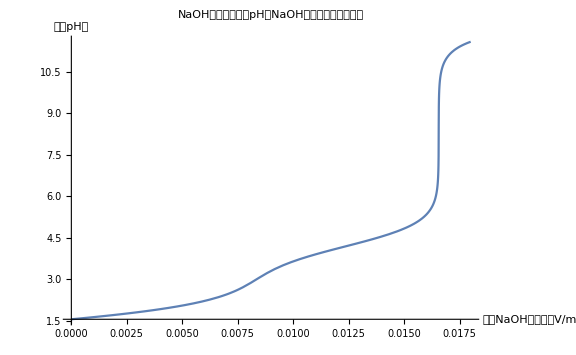

```mathematica
Plot[-Log10[IntegralH[{{{(0.02*0.04152)/(x+0.02),0,0},{10^-1.22,10^-4.19}},{{(-0.1003x)/(x+0.02),0},{1000}}}]],{x,0,0.018},AxesLabel->{"滴入NaOH溶液体积V/mL","溶液pH值"},PlotLabel->Style["NaOH滴定草酸溶液pH随NaOH滴入体积变化模拟图",15],ImageSize->Large]
```

```mathematica
-Log10[IntegralH[{{{0.05/(x+0.05),0,0},{10^-1.22,10^-4.19}},{{(-0.1x)/(x+0.05),0},{1000}}}/.x->1]]
```

8.43417

```mathematica
IntegralH[{{{3,2,3},{10^-3,10^-7}},{{0,4},{10^-8}}}]
```

1.17044×10^-7

```mathematica
x=16.56;
-Log10[IntegralH[{{{(0.02*0.04152)/(x+0.02),0,0},{10^-1.22,10^-4.19}},{{(-0.1000x)/(x+0.02),0},{1000}},{{0,0,(-0.00015x)/(x+0.02)},{4.2*10^-7,5.61*10^-11}}}]]
-Log10[IntegralH[{{{(0.02*0.04152)/(x+0.02),0,0},{10^-1.22,10^-4.19}},{{(-0.1003x)/(x+0.02),0},{1000}}}]]
Clear[x];
```

12.999

13.0003

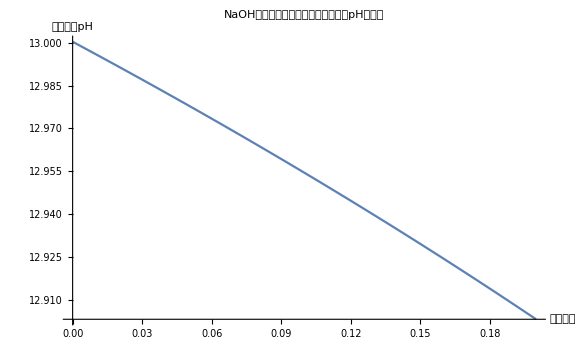

```mathematica
x=16.56;
Plot[-Log10[IntegralH[{{{(0.02*0.04152)/(x+0.02),0,0},{10^-1.22,10^-4.19}},{{(-(0.1003-y*0.1003)x)/(x+0.02),0},{1000}},{{0,0,(-y*0.1003x)/(x+0.02)},{4.2*10^-7,5.61*10^-11}}}]],{y,0,0.2},ImageSize->Large,AxesLabel->{"变质程度","滴定终点pH"},PlotLabel->Style["NaOH标准溶液变质程度对滴定终点的pH影响图",15]]
```

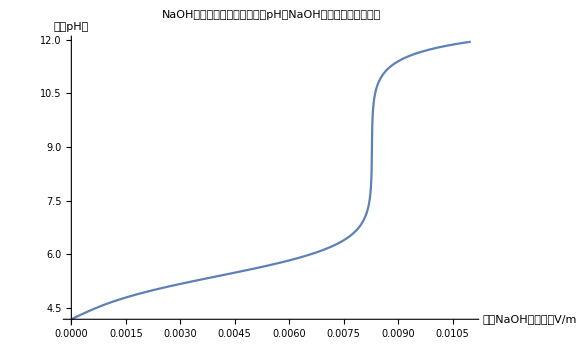

```mathematica
Clear[x];
Plot[-Log10[IntegralH[{{{0,(0.02*0.04152)/(x+0.02),0},{10^-2.95,10^-5.41}},{{(-0.1003x)/(x+0.02),0},{1000}}}]],{x,0,0.011},AxesLabel->{"滴入NaOH溶液体积V/mL","溶液pH值"},PlotLabel->Style["NaOH滴定邻苯二甲酸氢钾溶液pH随NaOH滴入体积变化模拟图",15],ImageSize->Large]
```

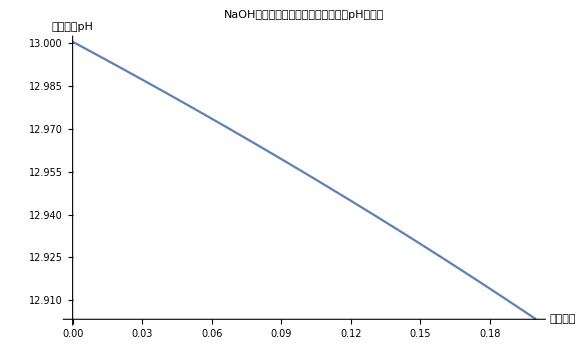

```mathematica
-Log10[ComplexH[{0.12,0},{10^-4.25}]]
```

2.59011

```mathematica
ProtonEquation[{1,2,1,3}]
```

{-13/7,-6/7,1/7,8/7}

```mathematica
ComplexH[{0.10,0,0},{5.9*10^-2,6.4*10^-5}]
```

0.0528454

```mathematica
Solve[D[#2&@@IonDistribution[x,{Ka1,Ka2}],x]==0,x]
```

{{x→-√Ka1 √Ka2},{x→√Ka1 √Ka2}}

```mathematica
IonDistribution[x,{Ka1,Ka2}]
```

{x^2/(Ka1 Ka2+Ka1 x+x^2),(Ka1 x)/(Ka1 Ka2+Ka1 x+x^2),(Ka1 Ka2)/(Ka1 Ka2+Ka1 x+x^2)}

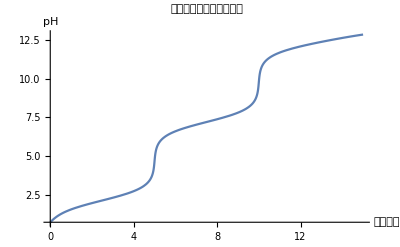

```mathematica
Plot[-Log10[IntegralH[{{{5/(1+x),0/(1+x),0/(1+x),0/(1+x)},{10^-2.12,10^-7.20,10^-12.32}},{{0,x/(1+x)},{0}}}]],{x,0,15},PlotRange->All,PlotLabel->"磷酸使用强碱滴定模拟图",AxesLabel->{"强碱体积","pH"}]
```

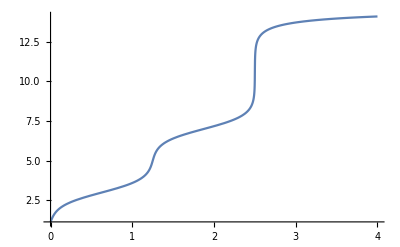

```mathematica
Plot[-Log10[IntegralH[{{{5/(1+x),0/(1+x),0/(1+x)},{10^-3,10^-7}},{{0,(4*x)/(1+x)},{0}}}]],{x,0,4},PlotRange->All]
```

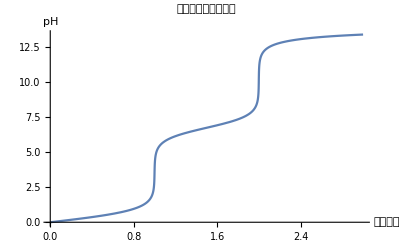

```mathematica
Plot[-Log10[IntegralH[{{{1/(1+x),0},{1000}},{{1/(1+x),0},{1.8*10^-7}},{{0,x/(1+x)},{0}}}]],{x,0,3},PlotRange->All,PlotLabel->"强酸与弱酸混合滴定",AxesLabel->{"强碱体积","pH"}]
```

```mathematica
KaListConvert[{1,10,100,1000}]
BetaListConvert[%]
```

{1,10,1000,1000000}

{1,10,100,1000}

```mathematica
BetaListConvert[%]
```

KaListConvert^(-1)

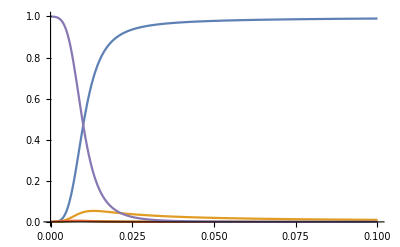

```mathematica
Plot[Evaluate@BetaIonDistribution[x,{1,100,100000,100000000}],{x,0,0.1}]
```

```mathematica
Coordination[ligand_,center_,BetaList_]:=Module[{x},x/.NSolve[-center*Table[i,{i,0,Length[BetaList]}].BetaIonDistribution[x,BetaList]+ligand==x,x]];
```

Plot::exclul: {1/((1+x) (1+First[{}]+10000 First[«1»]^2+10000000 First[«1»]^3+100000000000 First[«1»]^4))-0,(1+x)-0,Im[1/((1+x) (1+First[{}]+10000 Power[«2»]+10000000 Power[«2»]+100000000000 Power[«2»]))]-0} must be a list of equalities or real-valued functions.

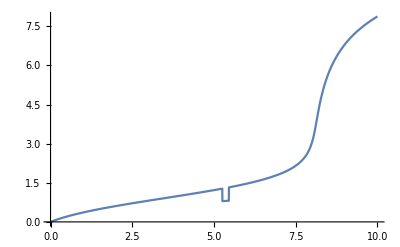

```mathematica
Plot[-Log10@Coordination[(0.5x)/(1+x),1/(1+x),{1,10000,10000000,100000000000}],{x,0,10}]
```

First::nofirst: {} has zero length and no first element.

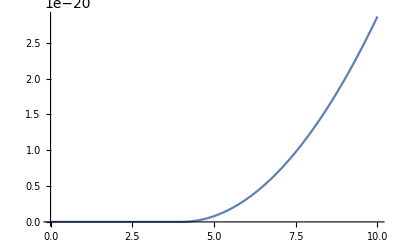

```mathematica
Plot[Coordination[x,2,{10^3.4,10^18}],{x,0,10}]
```

```mathematica
Plot[Coordination[x,2,{10^3.4,10^18}],{x,0,10}]
```

```mathematica
BetaIonDistribution[0.0001,{10^3.4,10^7.7}]
```

{0.570654,0.143342,0.286004}

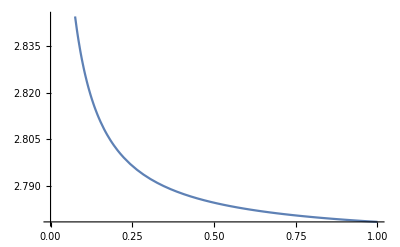

```mathematica
Plot[-Log10@ComplexH[{x,0,x},{5.6*10^-2,5.1*10^-5}],{x,0,1}]
```

```mathematica
Coordination1[ligand_,center_,BetaList_]:=Module[{x,list,a},list=x/.NSolve[center*(Table[-i,{i,0,Length[BetaList]}].BetaIonDistribution[x,BetaList])+ligand==x,x];
a=First[Select[Re@list,Positive]];
center*First[BetaIonDistribution[a,BetaList]]
]//Quiet;
```

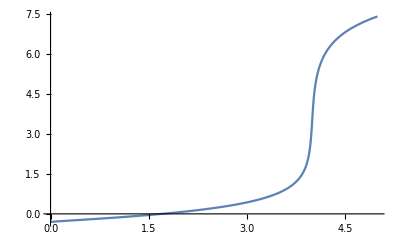

```mathematica
Plot[-Log10@Coordination1[x,2,{10^3.4,10^7.7}],{x,0,5}]
```

```mathematica
SubreactionIndex[ligand_,BetaList_]:=1/First@BetaIonDistribution[ligand,BetaList]
```

```mathematica
SubreactionIndex[0.1,10^#&/@{2.6,4.65,6.04,6.92,6.6,4.9}]
```

2455.63

```mathematica
ComplexCoordination[center_,BetaList_]:=
Module[{x,list1,list2,a},
list1=Table[A[i],{i,1,Length[BetaList]}];
list2=list1/.NSolve[center*(Table[-i,{i,0,Length[#1[[2]]]}].BetaIonDistribution[#2,#1[[2]]])+#1[[1]]&@@@Transpose[{BetaList,list1}]==list1,list1];
a=First[Select[Re@list2,Positive]]//Quiet;
center*First[BetaIonDistribution[a,BetaList]]
];
```

```mathematica
x/.NSolve[center*(Table[-i,{i,0,Length[BetaList]}].BetaIonDistribution[x,BetaList])+ligand==x,x]
```

```mathematica
Transpose[{{{1,{2,3}},{2,{3,4}}},{A[1],A[2]}}]
```

{{{1,{2,3}},A[1]},{{2,{3,4}},A[2]}}

```mathematica
NSolve[center*(Table[-i,{i,0,Length[#1[[2]]]}].BetaIonDistribution[#2,#1[[2]]])+#1[[1]]&@@@Transpose[{BetaList,list1}]==list1,list1]
```

```mathematica
Solve[{x1==x2==x3,x1==1},{x1,x2,x3}]
```

{{x1→1,x2→1,x3→1}}

```mathematica
Equal@@{x1,x2,x3}
```

x1==x2==x3

```mathematica
DebuggingComplexCoordination[center_,BetaList_]:=
Module[{x,list1,list2,
list1b,a},
list1=Table[A[i],{i,1,Length[BetaList]}];
list1b=Table[B[i],{i,1,Length[BetaList]}];
list2=list1/.NSolve[{Apply[Equal,list1b.(First[BetaIonDistribution[#2,#1[[2]]]]&@@@Transpose[{BetaList,list1}])],
Total[list1b]==center,list1b.((Table[-i,{i,0,Length[#1[[2]]]}].BetaIonDistribution[#2,#1[[2]]])+#1[[1]]&@@@Transpose[{BetaList,list1}])==list1},list1];
a=First[Select[Re@list2,Positive]]//Quiet;
center*First[BetaIonDistribution[a,BetaList]]
];
```

```mathematica
list1b.(First[BetaIonDistribution[#2,#1[[2]]]]&@@@Transpose[{BetaList,list1}])
```

```mathematica
Select[{{1,-1},{2,2}},Positive]
```

{}

```mathematica
Log10@SubreactionIndex[0.01,10^{3.2,7.0}]
```

3.00726

WolframAlphaQueryResults

0.00000000018

```mathematica
-Log10[1.8*10^-10]
```

9.74473

```mathematica
%-%243
```

6.73747

```mathematica
MetaChromatography[length_,DensityKList_,time_,speed_]:=Module[{initial,densitylist,klist,processlist},
densitylist=Transpose[DensityKList][[1]];
klist=Transpose[DensityKList][[2]];
initial=Transpose[Join[{{densitylist,Table[0,Length[densitylist]]}},Table[Table[Table[0,Length[DensityKList]],2],length]]];
processlist=initial;
Do[processlist={Join[Table[Table[0,Length[densitylist]],speed],Drop[#1,-speed]],#2}&@@Transpose[{(#1+#2)*1/(1+klist),(#1+#2)*klist/(1+klist)}&@@@Transpose[processlist]],time];
processlist];
ChromatographySimulation[length_,DensityKList_,time_,speed_]:=Module[{initial,densitylist,klist,processlist,simulist={}},
densitylist=Transpose[DensityKList][[1]];
klist=Transpose[DensityKList][[2]];
initial=Transpose[Join[{{densitylist,Table[0,Length[densitylist]]}},Table[Table[Table[0,Length[DensityKList]],2],length]]];
processlist=initial;
Do[processlist={Join[Table[Table[0,Length[densitylist]],speed],Drop[#1,-speed]],#2}&@@Transpose[{(#1+#2)*1/(1+klist),(#1+#2)*klist/(1+klist)}&@@@Transpose[processlist]];
AppendTo[simulist,Last[processlist[[1]]]];,time];
simulist];
ChromatographySimulationLog[length_,DensityKList_,time_,speed_]:=Module[{initial,densitylist,klist,processlist,log={}},
densitylist=Transpose[DensityKList][[1]];
klist=Transpose[DensityKList][[2]];
initial=Transpose[Join[{{densitylist,Table[0,Length[densitylist]]}},Table[Table[Table[0,Length[DensityKList]],2],length]]];
processlist=initial;
Do[processlist={Join[Table[Table[0,Length[densitylist]],speed],Drop[#1,-speed]],#2}&@@Transpose[{(#1+#2)*1/(1+klist),(#1+#2)*klist/(1+klist)}&@@@Transpose[processlist]];
AppendTo[log,processlist];,time];
log];
(*采取的数据结构为Transpose[{{{a1,b1,c1....}->液相中各组分浓度,{a2,b2,c2....}->固相中各组分浓度}->第一个格点,{{.....}},...}],即{{{a1,b1,c1,.....}->第一个格点的液相中各组分浓度,{a2,b2,c2,.....}->第二个格点的液相中各组分浓度,....},{{...},{...},....}->各个格点固相中的各组分浓度}}{*)
```

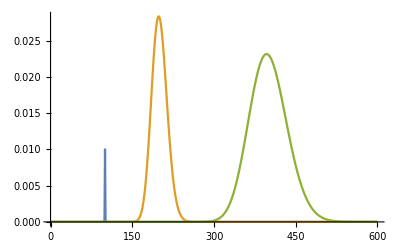

```mathematica
ListLinePlot[Transpose[ChromatographySimulation[100,{{0.01,0},{1,1},{2,3}},600,1]],PlotRange->All]
```

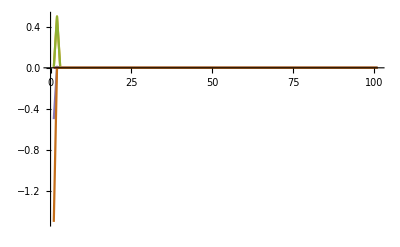

```mathematica
simulationlist=ChromatographySimulationLog[100,{{0.01,0},{1,1},{2,3}},600,1];
ListLinePlot[Join[Transpose[simulationlist[[1]][[1]]],-Transpose[simulationlist[[1]][[2]]]],PlotRange->All]
```

```mathematica
simulationlist2=ChromatographySimulationLog[100,{{0.01,0},{1,1},{2,3}},600,4];
ListLinePlot[Join[Transpose[simulationlist[[1]][[1]]],-Transpose[simulationlist[[1]][[2]]]],PlotRange->All]
```

-Graphics-

```mathematica
Export["simulation.gif",Animate[Row[{ListLinePlot[Join[Transpose[simulationlist[[i]][[1]]],-Transpose[simulationlist[[i]][[2]]]],PlotRange->All,ImageSize->Medium],
ListLinePlot[Transpose[First/@Last/@Transpose/@Take[simulationlist,i]],PlotRange->{{0,600},{0,0.03}},ImageSize->Medium]}],{i,1,600,1},AnimationRate->5]]
```

simulation.gif

```mathematica
Animate[Row[{ListLinePlot[Join[Transpose[simulationlist[[i]][[1]]],-Transpose[simulationlist[[i]][[2]]]],PlotRange->All,ImageSize->Medium],
ListLinePlot[Transpose[First/@Last/@Transpose/@Take[simulationlist,i]],PlotRange->{{0,600},{0,0.03}},ImageSize->Medium]}],{i,1,600,1},AnimationRate->5]
```

```mathematica
Animate[Row[{ListLinePlot[Join[Transpose[simulationlist2[[i]][[1]]],-Transpose[simulationlist2[[i]][[2]]]],PlotRange->All,ImageSize->Medium],
ListLinePlot[Transpose[First/@Last/@Transpose/@Take[simulationlist2,i]],PlotRange->{{0,150},{0,0.1}},ImageSize->Medium]}],{i,1,150,1},AnimationRate->5]
```

```mathematica
14+Log10/@Table[H[i*1.6*10^-6/145,{10^(-(14-4.63))}],{i,0,5}]//N
```

{7.,10.0214,10.1719,10.2599,10.3224,10.3709}